### Ground State Singlet and Triplet Potentials for ^23 Na_2 [Knoop et al., Phys. Rev. A 83, 042704 (2011)]

#### Single Atom Hyperfine and Zeeman Structure

```mathematica
Na23i = 3/2;
Na23s = 1/2; 
Na23gi = -0.00080461088;
Na23gs =  2.002319313470;
Na23AMHz =885.81306445;
amu = 1822.89;
massNa23 =22.98976928*amu;
μNa23 = massNa23/2;
```

```mathematica
μbMHz = (9.27*10^-24)/(6.626*10^-34)*10^-10;
Na23ATHz = Na23AMHz*10^-6;
Na23Ainvcm = (Na23ATHz *6.626*10^-34*10^12)/(1.986*10^-23);
Na23AH = Na23Ainvcm*invcminHartree;
μbTHz = μbMHz *10^-6;
μbinvcm = (μbTHz *6.626*10^-34*10^12)/(1.986*10^-23);
μbH=μbinvcm*invcminHartree;
```

```mathematica
Na23HFbasis = Flatten[Table[Table[{f, mf},{mf,-f,f}],{f,1,2}],1]
```

{{1,-1},{1,0},{1,1},{2,-2},{2,-1},{2,0},{2,1},{2,2}}

```mathematica
Hhf[A_,i_,s_,f_,ℏ_]:= A/2 ℏ^2(f(f+1)-s(s+1)-i(i+1));
Hz[fp_,mp_,f_,m_,gi_,gs_,s_,i_,B_]:= gs μbH B √((2 fp +1)(2f +1)) Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]-gi μbH B √((2 fp +1)(2f +1)) Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
```

```mathematica
HhfNa23Table=Table[Hhf[Na23AH,Na23i,Na23s,Na23HFbasis[[j,1]],1]KroneckerDelta[j,jp],{j,1,8},{jp,1,8}];
```

```mathematica
HzNa23Table[B_]= Table[Hz[Na23HFbasis[[jp,1]],Na23HFbasis[[jp,2]],Na23HFbasis[[j,1]],Na23HFbasis[[j,2]],Na23gi,Na23gs,Na23s,Na23i,B],{j,1,8},{jp,1,8}];
```

```mathematica
HNa23[B_]= HzNa23Table[B] + HhfNa23Table;
```

```mathematica
Na23AtomEigenSystem[B_]:=Sort[Transpose[Eigensystem[HNa23[B]]]]
Na23AtomEth[B_]:=Table[Na23AtomEigenSystem[B][[i]][[1]],{i,1,8}]
```

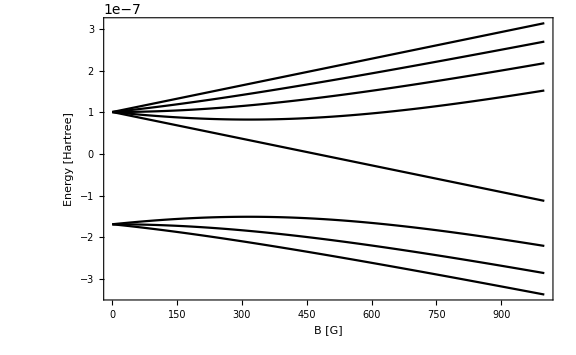

```mathematica
Plot[Na23AtomEth[B],{B,0,1000},Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},ImageSize->Large,LabelStyle->Large ]
```

### Singlet Potential

```mathematica
rsr = 2.181;
u1=-0.78531644*10^4;
u2 = 0.842586535*10^6;
rlr = 11.00;
b = -0.140;
rm = 3.0788576;
acf ={-6022.04193,−0.200727603516760356*10,0.302710123527149044*10^5,0.952678499004718833*10^4,−0.263132712461278206*10^5,−0.414199125447689439*10^5,0.100454724828577862*10^6,0.950433282843468915*10^5,−0.502202855817934591*10^7,−0.112315449566019326*10^7,0.105565865633448541*10^9,−0.626929930064849034*10^8,−0.134149332172454119*10^(10),0.182316049840707183*10^(10),0.101425117010240822*10^(11),−0.220493424364290123*10^(11),−0.406817871927934494*10^(11),0.144231985783280396*10^(12),0.379491474653734665*10^(11),
−0.514523137448139771*10^(12), 0.342211848747264038*10^(12),0.839583017514805054*10^(12),−0.131052566070353687*10^(13),−0.385189954553600769*10^(11),0.135760501276292969*10^(13),
−0.108790546442390417*10^(13),0.282033835345282288*10^(12)};
C6 = 0.75186131*10^7;
C8 = 0.1686430*10^9;
C10 = 0.3081961*10^10;
Aex = 0.40485835*10^5;
gamma = 4.59105;
beta = 2.36594;
Ns = 6;
```

```mathematica
ξ[r_]:= (r-rm)/(r+b rm);
uIR[r_]:= Sum[acf[[i+1]]*(ξ[r])^i,{i,0,Length[acf]-1}];
uSR[r_]:= u1 +u2/r^Ns;
uLR[r_]:= -C6/r^6-C8/r^8-C10/r^10-Aex r^gamma Exp[-beta r];
```

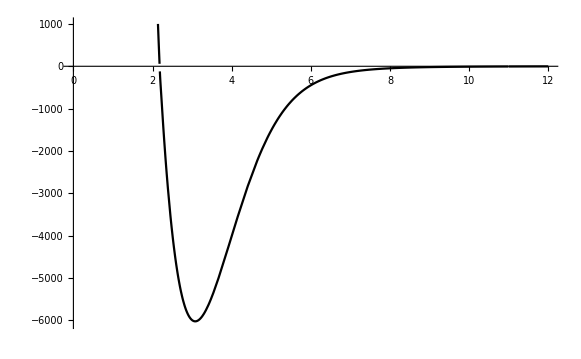

```mathematica
Singlet[r_]:=Piecewise[{{uSR[r],0<r≤rsr},{uIR[r],rsr<r<rlr},{uLR[r],rlr≤ r}}];
Plot[Singlet[r],{r,0,12},PlotRange->{-6050,1000}]
```

### Triplet Potential

```mathematica
rsr3=4.2780;
u13=-0.2435819*10^3;
u23=0.1488425*10^7;
b3 = -0.40;
rm3 =5.149085;
a3cf={−172.90517,0.355691862122135882*10,0.910756126766199941*10^3,−0.460619207631179620*10^3,0.910227086296958532*10^3,−0.296064051187991117*10^4,−0.496106499110302684*10^4,0.147539144920038962*10^5,−0.819923776793683828*10^4};
```

```mathematica
ξ3[r_]:= (r-rm3)/(r+b3 rm3);
uIR3[r_]:= Sum[a3cf[[i+1]]*(ξ3[r])^i,{i,0,Length[a3cf]-1}];
uSR3[r_]:= u13 +u23/r^Ns;
uLR3[r_]:= -C6/r^6-C8/r^8-C10/r^10+Aex r^gamma Exp[-beta r];
```

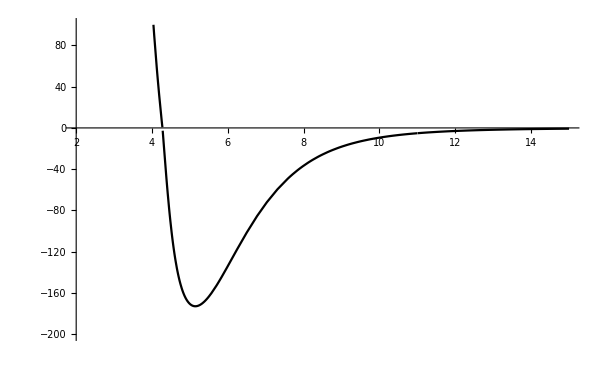

```mathematica
Triplet[r_]:=Piecewise[{{uSR3[r],0<r≤rsr3},{uIR3[r],rsr3≤ r≤ rlr},{uLR3[r],rlr≤ r}}];
Plot[{Triplet[r]},{r,2,15},PlotRange->{-200,100}]
```

#### Convert to Atomic Units

```mathematica
invcminHartree = 4.5563352812122295*10^-6;
AngstrominBohr = 1/0.529177210903;
Rmax=700;
Rmin=0.005;
NR =10000;
dR=(Rmax-Rmin)/NR;
RGrid =Table[Rmin+dR i,{i,1,NR}];
SingletNewdat = Table[{RGrid[[i]]*AngstrominBohr,Singlet[RGrid[[i]]]*invcminHartree},{i,1,NR}];
TripletNewdat = Table[{RGrid[[i]]*AngstrominBohr,Triplet[RGrid[[i]]]*invcminHartree},{i,1,NR}];
```

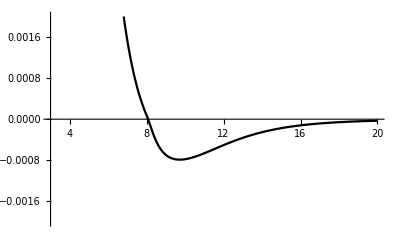

```mathematica
SingletNew = Interpolation[SingletNewdat];
TripletNew=Interpolation[TripletNewdat];
Plot[{(*SingletNew[r],*)TripletNew[r](*(-C6*AngstrominBohr^6*invcminHartree)/r^6-(C8*AngstrominBohr^8*invcminHartree)/r^8-(C10*AngstrominBohr^10*invcminHartree)/r^10*)},{r,3,20},PlotRange->{-0.002,0.002}]
```

#### Scattering Lengths

```mathematica
{Tripletascat,Tripletreff,TripletEREData}=CalcERETriplet[500,2,10^-14,10^-12,μNa23]
```

{64.5384,53.457,{{4.19078×10^-10,-0.0154946},{4.56795×10^-9,-0.0154945},{8.71683×10^-9,-0.0154944},{1.28657×10^-8,-0.0154943},{1.70146×10^-8,-0.0154942},{2.11634×10^-8,-0.0154941},{2.53123×10^-8,-0.015494},{2.94612×10^-8,-0.0154939},{3.36101×10^-8,-0.0154938},{3.77589×10^-8,-0.0154936},{4.19078×10^-8,-0.0154935}}}

```mathematica
{Singletascat,Singletreff,SingletEREData}=CalcERE[500,2,10^-14,10^-12,μNa23]
```

{19.9987,542.781,{{4.19078×10^-10,-0.0500032},{4.56795×10^-9,-0.0500021},{8.71683×10^-9,-0.050001},{1.28657×10^-8,-0.0499999},{1.70146×10^-8,-0.0499987},{2.11634×10^-8,-0.0499976},{2.53123×10^-8,-0.0499965},{2.94612×10^-8,-0.0499954},{3.36101×10^-8,-0.0499943},{3.77589×10^-8,-0.0499931},{4.19078×10^-8,-0.049992}}}

#### Hyperfine and Zeeman Structure for ^23 Na_2 with M_F=2

```mathematica
Na23MF2basis = {{1,1,1,1},{1,1,2,1},{1,0,2,2},{2,0,2,2},{2,1,2,1}};
Na23SingletProjection={{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,-3/16},{(√(3/2))/8,1/8,-1/(4 √2),1/(4 √2),-(√(3/2))/8},{-(√3)/8,-1/(4 √2),1/4,-1/4,(√3)/8},{(√3)/8,1/(4 √2),-1/4,1/4,-(√3)/8},{-3/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16}};
Na23TripletProjection={{13/16,-(√(3/2))/8,(√3)/8,-(√3)/8,3/16},{-(√(3/2))/8,7/8,1/(4 √2),-1/(4 √2),(√(3/2))/8},{(√3)/8,1/(4 √2),3/4,1/4,-(√3)/8},{-(√3)/8,-1/(4 √2),1/4,3/4,(√3)/8},{3/16,(√(3/2))/8,-(√3)/8,(√3)/8,13/16}};
```

```mathematica
HZ[f_,m_,fp_,mp_,s_,i_,gs_,gi_,A_,B_,μb_]:= A/2(f(f+1)-i(i+1)-s(s+1))KroneckerDelta[f,fp] KroneckerDelta[m,mp]+gs μb B Sqrt[(2fp+1)(2f+1)]Sum[ms ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp]-gi μb B Sqrt[(2fp+1)(2f+1)]Sum[mi ThreeJSymbol[{s, ms},{i, mi},{fp, -mp}]ThreeJSymbol[{s, ms},{i, mi},{f, -m}],{ms, -s,s},{mi,-i,i}]KroneckerDelta[m,mp];
HZsym[p_,l_,B_]:=Table[(1/(√((1+KroneckerDelta[Na23MF2basis[[j,1]],Na23MF2basis[[j,3]]] KroneckerDelta[Na23MF2basis[[j,2]],Na23MF2basis[[j,4]]])(1+KroneckerDelta[Na23MF2basis[[jp,1]],Na23MF2basis[[jp,3]]] KroneckerDelta[Na23MF2basis[[jp,2]],Na23MF2basis[[jp,4]]]))))*(HZ[Na23MF2basis[[j,1]],Na23MF2basis[[j,2]],Na23MF2basis[[jp,1]],Na23MF2basis[[jp,2]],Na23s,Na23i,Na23gs,Na23gi,Na23AH,B,μbH]KroneckerDelta[Na23MF2basis[[j,3]],Na23MF2basis[[jp,3]]]KroneckerDelta[Na23MF2basis[[j,4]],Na23MF2basis[[jp,4]]]+HZ[Na23MF2basis[[j,3]],Na23MF2basis[[j,4]],Na23MF2basis[[jp,3]],Na23MF2basis[[jp,4]],Na23s,Na23i,Na23gs,Na23gi,Na23AH,B,μbH]KroneckerDelta[Na23MF2basis[[j,1]],Na23MF2basis[[jp,1]]]KroneckerDelta[Na23MF2basis[[j,2]],Na23MF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[Na23MF2basis[[j,3]],Na23MF2basis[[j,4]],Na23MF2basis[[jp,1]],Na23MF2basis[[jp,2]],Na23s,Na23i,Na23gs,Na23gi,Na23AH,B,μbH]KroneckerDelta[Na23MF2basis[[j,1]],Na23MF2basis[[jp,3]]]KroneckerDelta[Na23MF2basis[[j,2]],Na23MF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[Na23MF2basis[[j,1]],Na23MF2basis[[j,2]],Na23MF2basis[[jp,3]],Na23MF2basis[[jp,4]],Na23s,Na23i,Na23gs,Na23gi,Na23AH,B,μbH]KroneckerDelta[Na23MF2basis[[j,3]],Na23MF2basis[[jp,1]]]KroneckerDelta[Na23MF2basis[[j,4]],Na23MF2basis[[jp,2]]]),{j,1,Length[Na23MF2basis]},{jp,1,Length[Na23MF2basis]}]
```

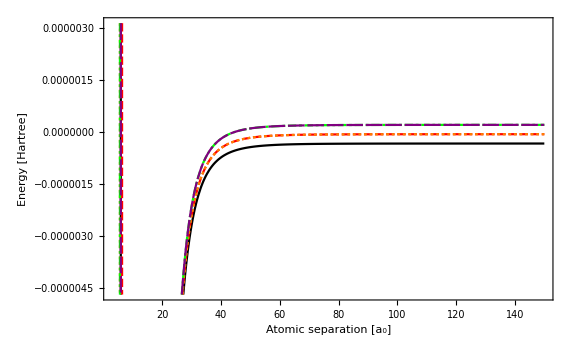

```mathematica
HZNa23[B_]=FullSimplify[HZsym[0,0,B]];
Htotal[r_,B_]= HZNa23[B]+Na23TripletProjection*TripletNew[r]+Na23SingletProjection*SingletNew[r];
Plot[{ Htotal[r, 0][[1, 1]], Htotal[r, 0][[2, 2]],Htotal[r, 0][[3, 3]],Htotal[r, 0][[4, 4]],Htotal[r, 0][[5, 5]]},{r,3,150},Frame->True,ImageSize->Large,FrameLabel->{"Atomic separation [a_0]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple}]
```

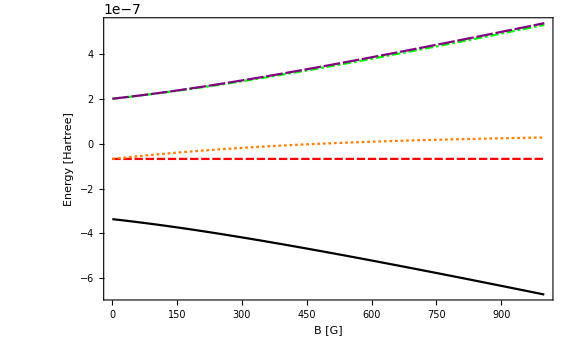

```mathematica
EigenSystemNa23[B_]:= Sort[Transpose[Eigensystem[HZNa23[B]]]];
Plot[{EigenSystemNa23[B][[1]][[1]],EigenSystemNa23[B][[2]][[1]],EigenSystemNa23[B][[3]][[1]],EigenSystemNa23[B][[4]][[1]],EigenSystemNa23[B][[5]][[1]]},{B,0,1000},ImageSize->Large,Frame->True,FrameLabel->{"B [G]","Energy [Hartree]"},LabelStyle->Large,PlotStyle->{Black,Red,Orange,Green,Purple}]
```

#### Van der Waals Units

```mathematica
(C6*invcminHartree*AngstrominBohr^6)
(C8*invcminHartree*AngstrominBohr^8)
(C10*invcminHartree*AngstrominBohr^10)
```

1560.08

124961.

8.15514×10^6

```mathematica
βNa23 = β/.Solve[(-C6*AngstrominBohr^6*invcminHartree)/β^6-(C8*AngstrominBohr^8*invcminHartree)/β^8-(C10*AngstrominBohr^10*invcminHartree)/β^10==-1/(2 μNa23 β^2),β][[8]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

90.1434

```mathematica
BohrinNa23vdw = 1/90.1434015057898
Na23vdwinHartree = 1/(2 μNa23 βNa23^2);
HartreeinNa23vdw = 1/Na23vdwinHartree
```

0.0110934

3.40536×10^8

```mathematica
C6vdw = (2 μNa23)/βNa23^4(C6*invcminHartree*AngstrominBohr^6)
C8vdw = (2 μNa23)/βNa23^6(C8*invcminHartree*AngstrominBohr^8)
C10vdw = (2 μNa23)/βNa23^8(C10*invcminHartree*AngstrominBohr^10)
```

0.990161

0.00976037

0.000078389

```mathematica
μbvdw = μbH*HartreeinNa23vdw;
```

```mathematica
TripletVDWdat= Table[{TripletNewdat[[i,1]]*BohrinNa23vdw, TripletNewdat[[i,2]]*HartreeinNa23vdw},{i,1,Length[TripletNewdat]}];
TripletVDW= Interpolation[TripletVDWdat];
SingletVDWdat= Table[{SingletNewdat[[i,1]]*BohrinNa23vdw, SingletNewdat[[i,2]]*HartreeinNa23vdw},{i,1,Length[SingletNewdat]}];
SingletVDW= Interpolation[SingletVDWdat];
```

```mathematica
Na23vlr[r_]:= -C6vdw/r^6-C8vdw/r^8-C10vdw/r^10;
```

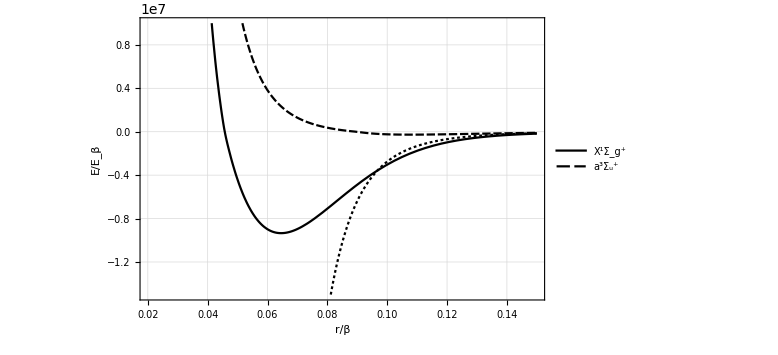

```mathematica
Plot[{SingletVDW[r],TripletVDW[r],Na23vlr[r]},{r,0.02,0.15},PlotRange->{-1.5*10^7,10^7},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"r/β","E/E_β"},LabelStyle->Medium,PlotLegends->{"X^1Σ_g^+","a^3Σ_u^+"}]
```

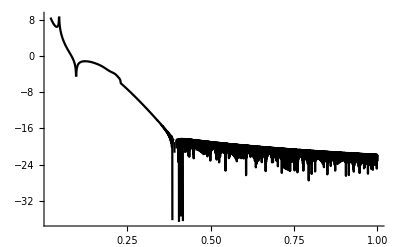

```mathematica
Plot[Log[Abs[(SingletVDW[r]-Na23vlr[r])/SingletVDW[r]]],{r,0.02,1}]
```

```mathematica
χminus[r_,l_]:= Sqrt[r] BesselJ[1/4(2l+1),1/(2 r^2) ];
χmprime[r_,l_]:= D[χminus[rp,l],rp]/.rp->r;
f[l_,k_,r_]:=r SphericalBesselJ[l,k r];
g[l_,k_,r_]:= r SphericalBesselY[l,k r];
dfdr[l_,k_,r_]:=D[f[l,k,rp],rp]/.rp->r; 
dgdr[l_,k_,r_]:=D[g[l,k,rp],rp]/. rp->r; 
basepairs[l_,ϕ_,α_,phaseint_,r_]:=Module[{αp,rp,f0,g0,f0p,g0p,χm,χmp},
αp=α';
g0=- α[r]Cos[ϕ+phaseint[r]];
f0= α[r]Sin[ϕ+phaseint[r]];
f0p=αp[r]/α[r] f0-1/α[r]^2 g0;
g0p=αp[r]/α[r] g0+1/α[r]^2 f0;
χm=χminus[r,l];
χmp=χmprime[r,l];
{f0,g0,f0p,g0p,χm,χmp}]
```

```mathematica
rx = 0.10;
rf = 3.0;
r0 = 0.4;
rmin = 2.0*BohrinNa23vdw;
rmax = r0;
ltest = 0;
Etest = 10^-16; 
ksqr[Ε_,l_,r_]:=(Ε - Na23vlr[r]-(l(l+1))/r^2);
BC1[Ε_,l_,r_,rx_]:=1/Sqrt[(Ε - Na23vlr[r]-(l(l+1))/r^2)^(1/2)]/.r->rx;
BC2[Ε_,l_,r_,rx_]:=D[1/Sqrt[(Ε - Na23vlr[r]-(l(l+1))/r^2)^(1/2)],r]/.r->rx;
α0sol=Flatten[Table[NDSolve[{α''[r]+ksqr[Etest,ltest,r]α[r]-1/α[r]^3==0,α[rx]==BC1[Etest,ltest,r,rx],α'[rx]==BC2[Etest,ltest,r,rx]},α,{r,rx,rf}],{ltest,0,2}]];
α0fun=Table[α/.α0sol[[i]],{i,1,Length[α0sol]}];
nr=300;rGrid=Table[rx+((i-1)/(nr-1))^3(rf-rx),{i,1,nr}];
PhaseIntTable=Table[Flatten[{0,Table[NIntegrate[(α0fun[[ltest+1]][rp])^-2,{rp,rGrid[[i-1]],rGrid[[i]]}],{i,2,nr}]}],{ltest,0,2}];
phaseintfun=Table[Interpolation[Table[{rGrid[[i]],Total[PhaseIntTable[[ltest+1,1;;i]]]},{i,1,nr}]],{ltest,0,2}];
phivals=Transpose[Table[Table[{f0,g0,f0p,g0p,χm,χmp}=basepairs[ltest,0.0,α0fun[[ltest+1]],phaseintfun[[ltest+1]],rf];{rf,ArcTan[-(χm g0p-χmp g0)/(χm f0p-χmp f0)]},{ltest,0,2}],{rf,rGrid}]];
ϕNa23=Table[phivals[[i,nr,2]],{i,1,Length[phivals]}];
```

```mathematica
ϕNa23[[1]]
```

-1.21368

```mathematica
CalcQuantumDefect[Ε_,l_,rmin_,rmax_,r0_,rx_,rf_,r_,nr_,U_,ϕ_]:= Module[{phaseint,αp,rp,αfun,α,f0,f0p,g0,g0p,u,up,Y,Ksr,mu},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,r0}];
αp=αfun';
f0=αfun[r0]Sin[ϕ+phaseint];
g0=-αfun[r0]Cos[ϕ+phaseint];
g0p=αp[r0]/αfun[r0] g0+1/αfun[r0]^2 f0;
f0p=αp[r0]/αfun[r0] f0-1/αfun[r0]^2 g0;
u=NDSolveValue[{-u''[r]+ (U[r]+(l(l+1))/r^2)u[r]==Ε u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
up=u';
Y = up[r]/u[r]/.r->r0;
Ksr = (Y f0 -f0p)/(Y g0 -g0p);
mu = 1/π ArcTan[Ksr];
Return[mu]
]
```

```mathematica
Na23SingletQD=CalcQuantumDefect[10^-16,0,rmin,rmax,r0,rx,rf,r,nr,SingletVDW,ϕNa23[[1]]]
Na23TripletQD=CalcQuantumDefect[10^-16,0,rmin,rmax,r0,rx,rf,r,nr,TripletVDW,ϕNa23[[1]]]
```

0.158449

-0.146683

```mathematica
Na23Avdw=Na23AH*HartreeinNa23vdw;
Na23HZVDW[p_,l_,B_]:=
Table[(1/(√((1+KroneckerDelta[Na23MF2basis[[j,1]],Na23MF2basis[[j,3]]] KroneckerDelta[Na23MF2basis[[j,2]],Na23MF2basis[[j,4]]])(1+KroneckerDelta[Na23MF2basis[[jp,1]],Na23MF2basis[[jp,3]]] KroneckerDelta[Na23MF2basis[[jp,2]],Na23MF2basis[[jp,4]]]))))*(HZ[Na23MF2basis[[j,1]],Na23MF2basis[[j,2]],Na23MF2basis[[jp,1]],Na23MF2basis[[jp,2]],Na23s,Na23i,Na23gs,Na23gi,Na23Avdw,B,μbvdw]KroneckerDelta[Na23MF2basis[[j,3]],Na23MF2basis[[jp,3]]]KroneckerDelta[Na23MF2basis[[j,4]],Na23MF2basis[[jp,4]]]+HZ[Na23MF2basis[[j,3]],Na23MF2basis[[j,4]],Na23MF2basis[[jp,3]],Na23MF2basis[[jp,4]],Na23s,Na23i,Na23gs,Na23gi,Na23Avdw,B,μbvdw]KroneckerDelta[Na23MF2basis[[j,1]],Na23MF2basis[[jp,1]]]KroneckerDelta[Na23MF2basis[[j,2]],Na23MF2basis[[jp,2]]]+(-1)^p(-1)^l HZ[Na23MF2basis[[j,3]],Na23MF2basis[[j,4]],Na23MF2basis[[jp,1]],Na23MF2basis[[jp,2]],Na23s,Na23i,Na23gs,Na23gi,Na23Avdw,B,μbvdw]KroneckerDelta[Na23MF2basis[[j,1]],Na23MF2basis[[jp,3]]]KroneckerDelta[Na23MF2basis[[j,2]],Na23MF2basis[[jp,4]]]+(-1)^p(-1)^l HZ[Na23MF2basis[[j,1]],Na23MF2basis[[j,2]],Na23MF2basis[[jp,3]],Na23MF2basis[[jp,4]],Na23s,Na23i,Na23gs,Na23gi,Na23Avdw,B,μbvdw]KroneckerDelta[Na23MF2basis[[j,3]],Na23MF2basis[[jp,1]]]KroneckerDelta[Na23MF2basis[[j,4]],Na23MF2basis[[jp,2]]]),{j,1,Length[Na23MF2basis]},{jp,1,Length[Na23MF2basis]}];
```

```mathematica
Na23HZ[B_]=FullSimplify[Na23HZVDW[0,0,B]];
Na23HVDW[r_,B_]=Na23HZ[B]+Na23TripletProjection*TripletVDW[r]+Na23SingletProjection*SingletVDW[r];
Na23Eigensystem[B_]:= Sort[Transpose[Eigensystem[Na23HZ[B]]]];
DD[B_]:= Transpose[{Na23Eigensystem[B][[1]][[2]],Na23Eigensystem[B][[2]][[2]],Na23Eigensystem[B][[3]][[2]],Na23Eigensystem[B][[4]][[2]],Na23Eigensystem[B][[5]][[2]]}];
Na23Eth[B_]:= Table[Na23Eigensystem[B][[j]][[1]],{j,1,5}];
```

```mathematica
KsrFTEI[B_]:= Transpose[DD[B]].Na23SingletProjection.DD[B]*Tan[π  Na23SingletQD] + Transpose[DD[B]].Na23TripletProjection.DD[B]*Tan[π Na23TripletQD]
```

```mathematica
KsrFTEIPP[B_]:= KsrFTEI[B][[1,1]];
KsrFTEIQP[B_]:=KsrFTEI[B][[2;;5,1]];
KsrFTEIPQ[B_]:=KsrFTEI[B][[1,2;;5]];
KsrFTEIQQ[B_]:=KsrFTEI[B][[2;;5,2;;5]];
```

```mathematica
En=200;
Emin = 10^-16;
Emax =15000;
EGrid=Table[Emin+((i-1)/(En-1))^3(Emax-Emin),{i,1,En}];
```

```mathematica
calcTanGamma[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{αfun,phaseint,g0,g0p,f0,f0p,αp,α,κ,rp,gbound,gboundp,tanγ},
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
κ=√-Ε;
gbound=√(κ/π rp) BesselK[l+1/2,κ rp]/.rp->rf;
gboundp=D[√(κ/π rp) BesselK[l+1/2,κ rp],rp]/.rp->rf;
tanγ =-(gbound g0p-gboundp g0)/(gbound f0p - gboundp f0);
Return[tanγ]
]
gammaTable=Table[{-EGrid[[ii]],ArcTan[calcTanGamma[0,rx,rf,r,-EGrid[[ii]],ϕNa23[[1]]]]},{ii,1,Length[EGrid]}];
```

```mathematica
GammaTablenew=gammaTable;
For[i=1,i<Length[gammaTable],i++,
If[(gammaTable[[i+1,2]]-gammaTable[[i,2]]<-1.2),Print[i];
GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]+π,GammaTablenew[[i+1;;En,2]]=GammaTablenew[[i+1;;En,2]]]
]
```

24

65

105

146

188

```mathematica
Gammafun = Interpolation[GammaTablenew(*,InterpolationOrder->1*)];
```

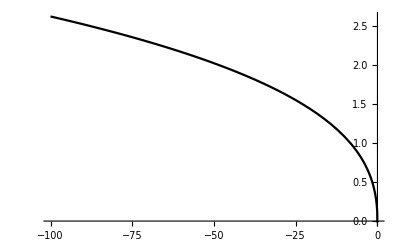

```mathematica
Plot[Gammafun[x],{x,0,-100}]
```

```mathematica
CotGamma2[B_,Ε_]:= Cot[Gammafun[((Na23Eth[B][[1]]+Ε)-Na23Eth[B][[2]])]];
CotGamma3[B_,Ε_]:= Cot[Gammafun[((Na23Eth[B][[1]]+Ε)-Na23Eth[B][[3]])]];
CotGamma4[B_,Ε_]:= Cot[Gammafun[((Na23Eth[B][[1]]+Ε)-Na23Eth[B][[4]])]];
CotGamma5[B_,Ε_]:= Cot[Gammafun[((Na23Eth[B][[1]]+Ε)-Na23Eth[B][[5]])]];
CotGammaMatrix[B_,Ε_]:=DiagonalMatrix[{CotGamma2[B,Ε],CotGamma3[B,Ε],CotGamma4[B,Ε],CotGamma5[B,Ε]}];
```

```mathematica
bmax = 1200;
bmin = 0;
bn = 500;
bgrid = Table[(bmax-bmin)/bn i,{i,0,bn}];
Etest = 10^-1;
KtildeFTEI[B_,Ε_]:= KsrFTEIPP[B]-KsrFTEIPQ[B].Inverse[KsrFTEIQQ[B]+CotGammaMatrix[B,Ε]].KsrFTEIQP[B];
```

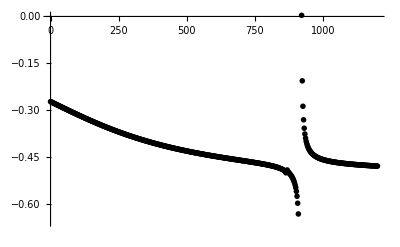

```mathematica
ListPlot[{Table[{bgrid[[ii]],KtildeFTEI[bgrid[[ii]],Etest]},{ii,1,bn+1}]},PlotStyle->{Black,Red}]
```

```mathematica
En2=100;
Emin2 = 10^-16;
Emax2=100;
EGrid2=Table[Emin2+((i-1)/(En2-1))^3(Emax2-Emin2),{i,1,En2}];
```

```mathematica
CalcTanEta[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,gs,fs,fsp,gsp,k,tanη,αfun,phaseint,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0=αfun[rf]Sin[ϕ+phaseint];
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs =g[l,k,r];
gsp=dgdr[l,k,r];
tanη=(fs f0p-f0 fsp)/(gs f0p-f0 gsp)/.r->rf;
Return[tanη]
]
EtaTable=Table[{EGrid2[[ii]],ArcTan[CalcTanEta[ltest,rx,rf,r,EGrid2[[ii]],ϕNa23[[1]]]]},{ii,1,Length[EGrid2]}];
```

```mathematica
EtaTablenew2=EtaTable;
For[i=1,i<Length[EtaTable],i++,
If[(EtaTable[[i+1,2]]-EtaTable[[i,2]]>1.2),Print[i];
EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]-π,EtaTablenew2[[i+1;;Length[EtaTable],2]]=EtaTablenew2[[i+1;;Length[EtaTable],2]]]
]
```

43

96

```mathematica
Etafun=Interpolation[EtaTablenew2,InterpolationOrder->1];
```

```mathematica
CalcA[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,fs,fsp,gs,gsp,k,A,αfun,phaseint,α,αp,tanη,Wfsf0,Wgsf0,Wfsg0,Wgsg0},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[Ε];
fs = f[l,k,rf];
fsp=dfdr[l,k,rf];
gs=g[l,k,rf];
gsp=dgdr[l,k,rf];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
A=-((Wfsg0 -tanη Wgsg0)/(Wgsf0+tanη Wfsf0));
Return[A]
]
```

```mathematica
ATable=Table[{EGrid2[[ii]],CalcA[ltest,rx,rf,r,EGrid2[[ii]],ϕNa23[[1]]]},{ii,1,Length[EGrid2]}];
```

```mathematica
Afun = Interpolation[ATable,InterpolationOrder->1]
```

InterpolatingFunction[…]

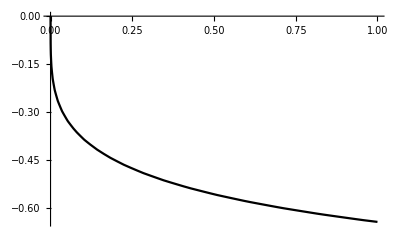

```mathematica
Plot[-Sqrt[Afun[ϵ]],{ϵ,0,1},PlotRange->{0,-1}]
```

```mathematica
CalcG[l_,rx_,rf_,r_,Ε_,ϕ_]:=Module[{f0,g0,f0p,g0p,χm,χmp,k,tanη,G,fs,fsp,gs,gsp,αfun,phaseint,Wfsf0,Wgsf0,Wfsg0,Wgsg0,α,αp},
(*{αfun,phaseint}= CalcAlphaPhaseIntFun[l,rx,rf,r,Ε];
{f0,g0,f0p,g0p,χm,χmp}=basepairs[l,ϕ,αfun,phaseint,r];*)
αfun = NDSolveValue[{α''[r] + ksqr[Ε,l,r]α[r] -1/α[r]^3== 0, α[rx] == BC1[Ε,l,r,rx],α'[rx] == BC2[Ε,l,r,rx]},α,{r,rx,rf}];
phaseint=NIntegrate[αfun[rp]^-2,{rp,rx,rf}];
αp=αfun';
f0=αfun[rf]Sin[ϕ+phaseint];
g0=-αfun[rf]Cos[ϕ+phaseint];
g0p=αp[rf]/αfun[rf] g0+1/αfun[rf]^2 f0;
f0p=αp[rf]/αfun[rf] f0-1/αfun[rf]^2 g0;
k = Sqrt[ Ε];
fs = f[l,k,r];
fsp=dfdr[l,k,r];
gs=g[l,k,r];
gsp=dgdr[l,k,r];
Wfsf0=fs f0p - fsp f0;
Wgsf0=gs f0p - gsp f0;
Wfsg0=fs g0p-fsp g0;
Wgsg0=gs g0p-gsp g0;
tanη=Wfsf0/Wgsf0;
G=-(Wfsg0*Wfsf0+Wgsg0*Wgsf0)/(Wfsf0^2+Wgsf0^2)/.r->rf;
(*G =-((g0 gsp-g0p gs)+tanη(g0 fsp-g0p fs))/((f0 gsp - f0p gs)+tanη (f0 fsp - f0p fs))/.r->rf;*)
Return[G]
]
GTable=Table[{EGrid2[[ii]],CalcG[ltest,rx,rf,r,EGrid2[[ii]],ϕNa23[[1]]]},{ii,1,Length[EGrid2]}];
```

```mathematica
Gfun =Interpolation[GTable,InterpolationOrder->1];
```

```mathematica
Etest =10^-3;
KFTEITable = Table[{bgrid[[ii]], Sqrt[Afun[Etest]] (KtildeFTEI[bgrid[[ii]],Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]]},{ii,1,bn+1}];
```

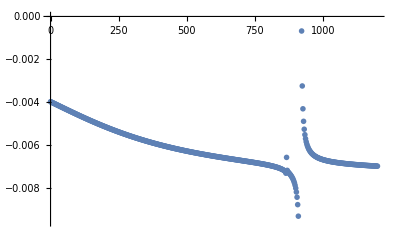

```mathematica
ListPlot[{KFTEITable}]
```

```mathematica
KFTEIfun[B_,Etest_]:= Sqrt[Afun[Etest]](KtildeFTEI[B,Etest]^-1+Gfun[Etest])^-1 Sqrt[Afun[Etest]];
Sfun[B_,Etest_]:= Exp[ⅈ Etafun[Etest]] ((1+ⅈ KFTEIfun[B,Etest])/(1-ⅈ KFTEIfun[B,Etest])) Exp[ⅈ Etafun[Etest]];
ascatfun[B_,Etest_]:= -1/(ⅈ Sqrt[Etest]) ((Sfun[B,Etest]-1)/(Sfun[B,Etest]+1));
```

```mathematica
cotdeltafun[Ε_,B_]:=(1-Tan[Etafun[Ε]]KFTEIfun[B,Ε])/(Tan[Etafun[Ε]]+KFTEIfun[B,Ε]);
```

```mathematica
CalcERE[ΕMin_,ΕMax_,Btest_]:=
Module[{EREData,ascat,reff,A,B,fitpars,dE},
dE=(ΕMax-ΕMin)/10;
EREData=Table[{ Εtest,√Εtest cotdeltafun[Εtest,Btest]},{Εtest,ΕMin,ΕMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
mqdtresdat =Table[{B, CalcERE[10^-3,10^-1,B][[1]]},{B,0,1000,1}];
```

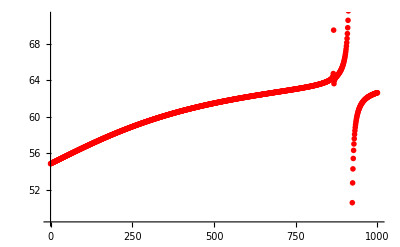

```mathematica
p10=ListPlot[Table[{mqdtresdat[[i,1]],mqdtresdat[[i,2]]*1/BohrinNa23vdw},{i,1,Length[mqdtresdat]}],PlotStyle->Red]
```

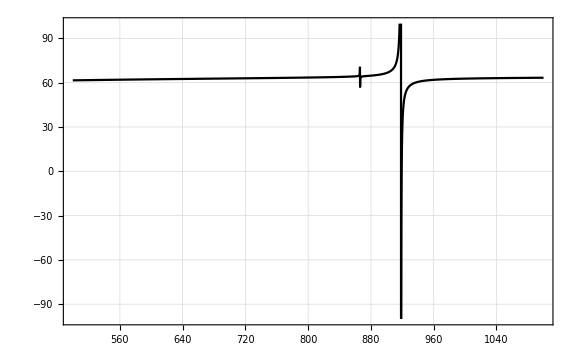

```mathematica
p15= Plot[{ascatfun[B,10^-2]*1/BohrinNa23vdw},{B,500,1100},Frame->True,GridLines->Automatic,ImageSize->Large,PlotStyle->{Red,Black},PlotRange->{-100,100}]
```